# Majorana Hamiltonian Exact Diagonalization (ED)

## The Gamma-Operator Generator Cell

-Graphics-

```mathematica
(*Higher Dimensional Gamma Matrices*)

(*This cell calculates the Gamma matrices using the above procedure, which is used in the Majorana Hamiltonians*)

(*n=Dimensions, Even Numbers*)
n=44;


(* Pauli Matrix Group = {I,Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]} *) 
(*Defined As a Sparse Matrix*)
PauliMatrixGroup = {SparseArray[IdentityMatrix[2]],SparseArray[PauliMatrix[1]],SparseArray[PauliMatrix[2]],SparseArray[PauliMatrix[3]]};

(*Gamma Matrices Indecies- List of the indecies of Pauli Matrices needed from PauliMatrixGroup to make GML*)
GMI={};
For[i=0,i<n/2, i++,{
kk=1;
Llist={};

For[j=0,j<n, j++,{

If[j<2 i,AppendTo[Llist,1 ],
(*Else:*)
kk+=1;
If[kk>4,kk=4];
AppendTo[Llist,kk ]
 ]
}];
AppendTo[GMI,Llist]
}]
GMI=Transpose[GMI];



(* Gamma Matrices List*)
GML={};

For[i=1,i<=n,i++,{

(* We go from the last to the first, kronecker producting all*)
A= PauliMatrixGroup[[ GMI[[i,(n/2)]] ]] ;

For [j=(n/2)-1,j>0,j--,{

A= KroneckerProduct[PauliMatrixGroup[[ GMI[[i,j]] ]],A  ] ;

}];
AppendTo[GML,A];
}]

(*The List to Get the Gamma Matrices are
GML[[4]]//MatrixForm
*)

For[i=1,i<=n,i++,{Subscript[γ, i]=GML[[i]]}]
ClearAll[GML];
(*Matrices are available as Subscript[γ, i] for i∈[1,n] *)
```

## Building The Hamiltonian -Graphics-

```mathematica
(*This Cell Calculates the Hamiltonian using the above gamma Matrices. Cells should be executed in order.*)
(*The Above Hamiltonian, is an example of a Majorana Hamiltonian, referred to as the "Ian Model", throughout the code. See more at:
https://arxiv.org/abs/1504.05192
Also, There's an option for a similiar model, refferred to as the "OF Model". read more from O'brien & Fendley's paper:
https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.206403
*)

PBC=True; (*True=Anti-Periodic Boundary COndition , False=Open Boundary Conditiotn*)
OF=True; (*OF Model or not*)

AbsoluteTiming[
(*Building The Hamiltonian*)
H=SparseArray[{},{2^(n/2),2^(n/2)}];

(*In case of a parametric calculation, comment out these lines*)
(*Parameters used in the Hamiltonian*)
Clear[t,g];
t=-0.428;
g=1;

(*Two-Site First-Neighbour Interaction*)
For[i=1,i<n,i++,
{
H+= I t   Subscript[γ, i].Subscript[γ, i+1];
}];

(*Four-Site Interaction*)
If[OF==False,
(*Ian Model*)
{For[i=1,i<n-3,i++,

H+= g Subscript[γ, i].Subscript[γ, i+1].Subscript[γ, i+2].Subscript[γ, i+3] ;
]}
,
(*OF Model*)
{For[i=1,i<n-4,i++,

H+= g Subscript[γ, i].Subscript[γ, i+1].Subscript[γ, i+3].Subscript[γ, i+4] ;
]};
]
Print["Non-Boundary Calculations Done!"];



(*Boundary Condition*)
If[PBC==True,
If[OF==False,
H+= - I t   Subscript[γ, n].Subscript[γ, 1]-g Subscript[γ, n-2].Subscript[γ, n-1].Subscript[γ, n].Subscript[γ, 1] +g Subscript[γ, n-1].Subscript[γ, n].Subscript[γ, 1].Subscript[γ, 2] -g Subscript[γ, n].Subscript[γ, 1].Subscript[γ, 2].Subscript[γ, 3]; (*Ian Model*)
,
H+= - I t   Subscript[γ, n].Subscript[γ, 1]-g Subscript[γ, n-3].Subscript[γ, n-2].Subscript[γ, n].Subscript[γ, 1] +g Subscript[γ, n-2].Subscript[γ, n-1].Subscript[γ, 1].Subscript[γ, 2] +g Subscript[γ, n-1].Subscript[γ, n].Subscript[γ, 2].Subscript[γ, 3] -g Subscript[γ, n].Subscript[γ, 1].Subscript[γ, 3].Subscript[γ, 4] ;(*OF Model*)
 ]
] 

Print["Hamiltonian Calculated! Estimated Time of Calculation:"];

][[1]]
```

## Calculating The Eigenvalues/Eigenvectors

```mathematica
(*Calculating the first m Eigenvalues*)

(*In case of Parametric Calculations*)
t=-0.428;
g=1;
m=10;(*Number of highest (in magnitude) energy levels needed*) 

Print["n=",n];
Print["Approximate time taken:"];
AbsoluteTiming[EV=Eigenvalues[N[H],m]][[1]]
Print[EV];
```

## Visualizing EV

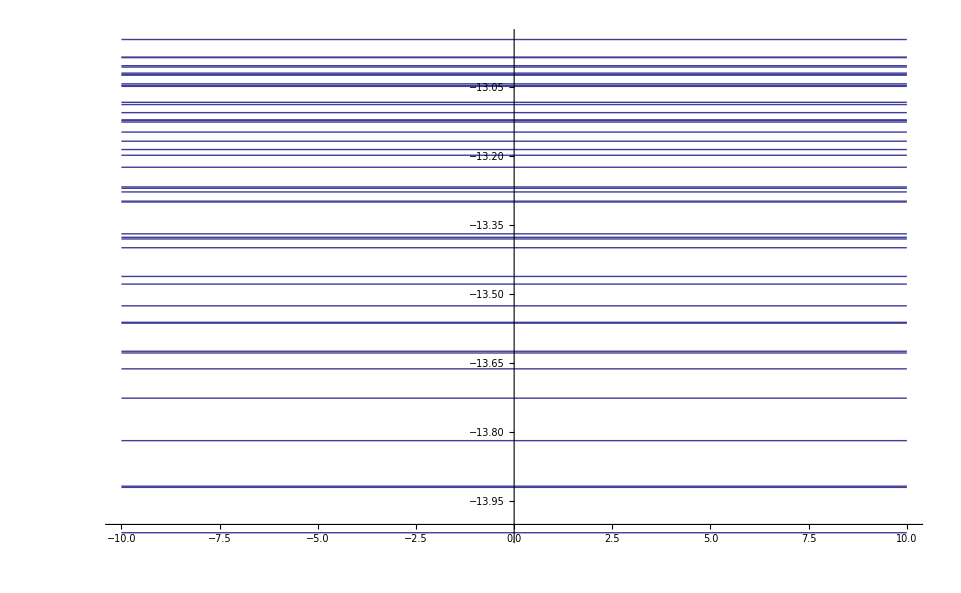

```mathematica
EV1={};
For[i=1,i<50,i++,
If[EV[[i]]<0,AppendTo[EV1,EV[[i]]]];]

Plot[EV1/RF,{x,-10,10}(*,PlotStyle->{Thick}PlotRange->{-28.6,-29}*)]
```

## Defining the Fermion Parity Operator -Graphics-

```mathematica
(*Fermion Parity*)
F=IdentityMatrix[2^(n/2) , SparseArray];
For[i=1, i≤ n,i+=2,
F= I F.Subscript[γ, i].Subscript[γ, i+1];
]
```

## EigenVectors + Fermion Parity

-40.4673{{1.}}

-35.0742{{-1.}}

-35.0742{{-1.}}

-35.0714{{1.}}

-30.14{{1.}}

-30.14{{1.}}

29.4482{{-1.}}

29.4482{{-1.}}

-27.9527{{-1.}}

-27.9527{{-1.}}

-27.2472{{1.}}

-26.9826{{-1.}}

-26.9826{{-1.}}

-26.9071{{-1.}}

-26.9071{{-1.}}

26.8939{{-1.}}

26.8939{{-1.}}

-26.7877{{-1.}}

-26.7877{{-1.}}

-26.3534{{1.}}

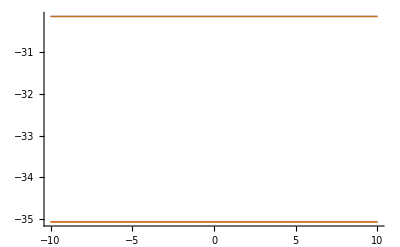

```mathematica
(*Eigen Vectors & Values+*)
t=1;
g=2.46;
EValues =Eigenvalues[N[H]];
EVectors=Eigenvectors[N[H]];


For[i=1,i≤ n,i++,
EVec= EVectors[[i]];
EVal=EValues[[i]];
Parity ={EVec}.F.ConjugateTranspose[{EVec}];(*1=Even/Bosons,-1=Odd/Fermions*)
Print[EVal,Parity];
]
Plot[EValues,{x,-10,10},PlotStyle->{Thick},PlotRange->{-30,-40}]
```